```mathematica
f[x_]:=x^2
intF[h_]:=NIntegrate[Exp[f[x]+I*x],{x,-h,h}]
slope[h_]:=Exp[f[0]]*2*Sinh[h*(f'[0]+I)]/(f'[0]+I)
midPoint[h_]:=2*h*Exp@f@0
hist[h_]:=NIntegrate[Exp[f[x]],{x,-h,h}]/h*Sin[h]
```

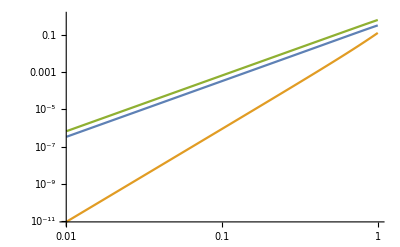

```mathematica
LogLogPlot[{-Re@midPoint[h]+Re@intF[h],Re@hist[h]-Re@intF[h],-Re@slope[h]+Re@intF[h]},{h,.01,1}]
```

```mathematica
exact[h_]:=Series[Log[Integrate[Exp[γ[x]+g[x]],{x,-h,h}]/(2h)],{h,0,4}]//FullSimplify
```

```mathematica
exact[h]
```

Log[ⅇ^(g[0]+γ[0])]+1/6 ((g'[0]+γ'[0])^2+g''[0]+γ''[0]) h^2+1/360 (-2 g'[0]^4-8 g'[0]^3 γ'[0]-2 γ'[0]^4+8 γ'[0]^2 (g''[0]+γ''[0])+4 (g''[0]+γ''[0])^2+g'[0]^2 (-12 γ'[0]^2+8 (g''[0]+γ''[0]))+12 γ'[0] (g^(3)[0]+γ^(3)[0])+4 g'[0] (-2 γ'[0]^3+4 γ'[0] (g''[0]+γ''[0])+3 (g^(3)[0]+γ^(3)[0]))+3 (g^(4)[0]+γ^(4)[0])) h^4+O[h]^5

```mathematica
Series[γ[0]g[0]-exact[h],{h,0,3}]//FullSimplify
Series[Log[Integrate[Exp[γ[x]],{x,-h,h}]Exp[g[0]]/(2h)]-exact[h],{h,0,3}]//FullSimplify
Series[Log[Integrate[Exp[γ[x]],{x,-h,h}]Integrate[Exp[g[x]],{x,-h,h}]/(2h)^2]-exact[h],{h,0,3}]//FullSimplify
Series[Log[Integrate[Exp[γ[0]+γ'[0]x+g[x]],{x,-h,h}]/(2h)]-exact[h],{h,0,3}]//FullSimplify
```

(-Log[ⅇ^(g[0]+γ[0])]+g[0] γ[0])+1/6 (-(g'[0]+γ'[0])^2-g''[0]-γ''[0]) h^2+O[h]^4

(-1/6 g'[0] (g'[0]+2 γ'[0])-g''[0]/6) h^2+O[h]^4

-1/3 (g'[0] γ'[0]) h^2+O[h]^4

-1/6 γ''[0] h^2+O[h]^4

```mathematica
Series[Log[Integrate[Exp[γ[x]],{x,-h,h}]Integrate[Exp[g[x]],{x,-h,h}]/(2h)^2],{h,0,4}]//FullSimplify
```

Log[ⅇ^(g[0]+γ[0])]+1/6 (g'[0]^2+γ'[0]^2+g''[0]+γ''[0]) h^2+1/360 (-2 g'[0]^4-2 γ'[0]^4+8 g'[0]^2 g''[0]+4 g''[0]^2+8 γ'[0]^2 γ''[0]+4 γ''[0]^2+12 g'[0] g^(3)[0]+12 γ'[0] γ^(3)[0]+3 (g^(4)[0]+γ^(4)[0])) h^4+O[h]^5

```mathematica
Series[Log[Integrate[Exp[a*x+b/2x^2+c/6x^3],{x,-h,h}]Integrate[Exp[(a+t)*x],{x,-h,h}]/Integrate[Exp[a*x],{x,-h,h}]/(2h)],{h,0,6}]-exact[h]//FullSimplify
```

-1/90 (t (4 a b+3 c+2 b t)) h^4+(t (16 a^3 b-2 b^2 t+9 a c t+3 c t^2+3 a^2 (3 c+8 b t)-4 a b (b-4 t^2)+4 b (-3 c+t^3)) h^6)/1890+O[h]^7

```mathematica
Series[Log[Tan[x]],{x,0,10}]
```

Log[x]+x^2/3+(7 x^4)/90+(62 x^6)/2835+(127 x^8)/18900+(146 x^10)/66825+O[x]^11

```mathematica
Integrate[Exp[(a+t)*x],{x,-h,h}]/Integrate[Exp[a*x],{x,-h,h}]//FullSimplify
```

(a Csch[a h] Sinh[h (a+t)])/(a+t)

```mathematica
qmEvol[t_]:=2Cosh[t](*Only the case for periodic boundaries*)
propFac[t_,n_]:=(Sinh[2t/n]/2)^(n/2)
classicPartition[h_,n_]:=2^n (Cosh[h]^n+Sinh[h]^n)
qToCl[t_,n_]:=-1/2Log@Tanh[t/n]
statPower[t_,n_]:=classicPartition[h,n]/classicPartition[Re@h,n]/.h->qToCl[t,n]
```

```mathematica
Manipulate[Plot[{Re@qmEvol[I t],propFac[I t,n]classicPartition[qToCl[I t,n],n]//Re},{t,0,10}],{{n,2},0,10,1}]
```

```mathematica
Manipulate[LogPlot[{Abs[statPower[I t,n]]^l,Exp[-t^2/2/(Pi/4)^2*l],Exp[-l t]},{t,0,20},PlotRange->{10^-10,1}],{{n,10},1,2000,1},{{l,10},1,100,1}]
```

```mathematica
Exp[-6*12*Pi/4]//N
```

2.76201×10^-25

```mathematica
Manipulate[LogPlot[{(propFac[I t,n]classicPartition[Re@qToCl[I t,n],n]//Abs)^l/.h->-1/2Log@Tanh[I t/n],Exp[l t]},{t,0,20},PlotRange->{1,10^15}],{{n,10},1,2000,1},{{l,10},1,100,1}]
```

```mathematica
statPower[I 1.,4]^4
```

0.0372512+0. ⅈ